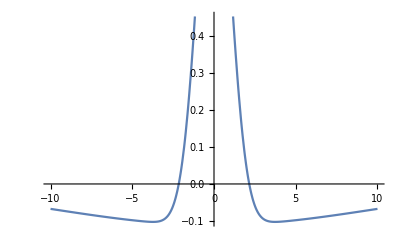

-Graphics-

```mathematica
s:=1;
t:= 10;

wfunc[z_]:=(t*Exp[-z^2/(2*s^2)]-s*Exp[-z^2/(2*t^2)])/(t-s);
Plot[wfunc[z],{z,-10,10}]



Ffunc[k_]=Integrate[w[z]*Cos[k*z],{z,-10,10}];



Plot[Ffunc[k],{k,-1,1}]
```